```mathematica
(*System Parameters*)

L=3.5;
V0=(*4.0*)7.2912229;
U0=(*40.0*)-1.0;
r=0.005;
(*alpha=16*)

alpha=22;
num=alpha+(alpha*(alpha-1))/2;
Print["Truncation = ",num];

Kdel[i_,j_]:=If[i==j,1,0];
Classical[x_]:=U0/(r*√(2*π))*Exp[-x^2/(2*r^2)];
(*Single Particle in a box states*)
psi[n_,x_]:=1/(√L)Sin[(n*π)/2(x/L-1)];


(*Single Particle Energy Levels*)

psqdiag[m_]:=(m^2 π^2)/(4 L^2);
xsq[n_,m_]:=(32*m*n)/(π^2(m^2-n^2)^2)L^2;
xsqrdiag[n_]:=(1/3-2/(n^2 π^2))L^2;
xfr[n_,m_]:=(64*m*n)/π^4(π^2/((m^2-n^2)^2)-(48*(m^2+n^2))/((m^2-n^2)^4))L^4;
xfrdiag[n_]:=(1/5-4/(n^2 π^2)+24/(n^4 π^4))L^4;
               Honep=Table[If[n==m,psqdiag[m]+V0*(-2xsqrdiag[m]+xfrdiag[m])
                                             ,
                                               If[EvenQ[n+m],V0*(-2xsq[n,m]+xfr[n,m])
                                                   ,
                                                     0]],{m,1,num},{n,1,num}];
        

Print["Single Particle Energy Levels Plotted, ground state="];

Oneparticlelevels=Sort[Eigensystem[Honep][[1]]];

Print["Diagonalizing two particle hamiltonian..."];


(*Tower of 2-particle states*)
statetower=Table[0,{nt,1,num}];
count=0;
For[i=1,i≤alpha,i++,
      For[j=1,j≤i,j++,
             statetower[[count+1]]={i,j};
             count=count+1;
           ]
   ]
(*
En=Table[statetower[[i,1]]^2+statetower[[i,2]]^2,{i,1,count}];
For[i=1,i≤count,i++,
       For[j=1,j<i,j++,
    
         If[En[[i]]<En[[j]],
                       {En[[i]],En[[j]]}={En[[j]],En[[i]]};
                     {statetower[[i]],statetower[[j]]}={statetower[[j]],statetower[[i]]};

                   ,Continue]
           ]
    ] REDUNDANT?*)




Pot[n_,m_]:=If[EvenQ[m+n],If[m==n,V0*(-2*xsqrdiag[n]+xfrdiag[n]),V0*(-2*xsq[m,n]+xfr[m,n])],0.0];


(*Now, to build the matrix elements of 2 Bosons in a double well WITH BOSONIZATION*)


H=Table[0.0,{nt,1,num},{mt,1,num}];

For[nt=1,nt≤num,nt++,
       For[mt=1,mt≤nt,mt++,
             
n1=statetower[[nt,1]];
n2=statetower[[nt,2]];
m1=statetower[[mt,1]];
m2=statetower[[mt,2]];
n3=m1;
n4=m2;
            
 noninteracting=(n1^2+n2^2)/(4 L^2)π^2*(Kdel[m1,n1]Kdel[m2,n2]+Kdel[m1,n2]Kdel[m2,n1])+Pot[n1,m1]*Kdel[n2,m2]+Pot[n1,m2]*Kdel[n2,m1]+Pot[n2,m1]*Kdel[n1,m2]+Pot[n2,m2]*Kdel[n1,m1];
   
(*INTERACTION MATRIX ELEMENTS*)
term1=1.0/(4.0*L);
    term2=1.0/(2.0*L);
    term3=3.0/(4.0*L);

interelement=0.0;
If[(n1-n2)==(n3+n4),
     If[(n1-n2)==0, interelement=term2, interelement=-term1],Continue]

     If[(n1+n2)==(n3+n4),
     If[(n1+n2)==0, interelement=term2, interelement=term1],Continue]

     If[(n1-n2)==(n4-n3),
     If[(n1-n2)==0, interelement=term2, interelement=term1],Continue]

     If[(n1+n2)==(n4-n3),
     If[(n1+n2)==0,interelement=term2,interelement=-term1],Continue]

     If[(n1-n2)==(n3-n4),
     If[(n1-n2)==0,interelement=term2,interelement=term1],Continue]

     If[(n1+n2)==(n3-n4),
     If[(n1+n2)==0,interelement=term2,interelement=-term1],Continue]

     If[(n1-n2)==(-n3-n4),
     If[(n1-n2)==0,interelement=term2,interelement=-term1],Continue]

     If[(n1+n2)==(-n3-n4),
     If[(n1+n2)==0,interelement=term2,interelement=term1],Continue]

     If[(n1==n2)&&(n3==n4)&&(n2==n3),interelement=term3,Continue];

    interelement=2.0*interelement;

H[[nt,mt]]=Re[(noninteracting+U0*interelement)/Sqrt[(1+Kdel[n1,n2])*(1+Kdel[m1,m2])]];

H[[mt,nt]]=H[[nt,mt]];
     
    
]
]




(*Eigenvalues & eigenvector Coefficients in the 2-Bosons in a box representation*)

Coeff=Table[0.0,{i,1,num}];

Energies=Eigensystem[H][[1]];

For[stateno=1,stateno≤num,stateno++,Coeff[[stateno]]=Eigensystem[H][[2,stateno]]];

SortedEnergies=Energies;
SortedCoeff=Coeff;

(*Sort eigenvectors in increasing order of eigenvalue*)

For[i=1,i≤num,i++,
     For[j=i,j≤num,j++,

       If[SortedEnergies[[i]]>SortedEnergies[[j]],
            temp=SortedEnergies[[i]];
            SortedEnergies[[i]]=SortedEnergies[[j]];
          SortedEnergies[[j]]=temp;
        temp2=SortedCoeff[[i]];
     SortedCoeff[[i]] =SortedCoeff[[j]];
SortedCoeff[[j]]=temp2;      
    
,Continue]


]
]



Print["Unperturbed 2-Particle Energies, ground state="];

SortedEnergies[[1]]

E1=SortedEnergies[[1]];
E2=SortedEnergies[[2]];
E4=SortedEnergies[[4]];
E7=SortedEnergies[[7]];
Detuning=0;
wfndet=E4-E2;
wsndet=E2-E1;
wf=wfndet-Detuning;
ws=wsndet+Detuning;
wf/ws
```

Truncation = 253

Single Particle Energy Levels Plotted, ground state=

Diagonalizing two particle hamiltonian...

Unperturbed 2-Particle Energies, ground state=

-6.42262

8.625

```mathematica
c
```

6.

```mathematica
wf
ws
Detuning
wf/ws
Period=Pi*(69/wf+8/ws)
w=2*Pi/Period
```

6.32889

0.733784

0

8.625

68.5017

0.091723

```mathematica
SortedEnergies
Oneparticlelevels
```

{-6.42262,-5.68883,-4.33098,0.640055,1.75299,6.00615,6.96998,7.79352,12.8946,13.0175,13.9536,18.4657,19.9255,20.6015,21.6044,25.2604,27.6678,29.0103,30.0326,32.1867,32.9706,36.0833,38.0757,39.0729,39.7791,41.4274,45.1548,47.5095,47.9187,48.2523,48.9478,50.4678,54.9802,55.8387,57.3407,58.1098,59.1197,60.3305,64.3091,64.9646,65.1719,67.1753,68.9099,69.9293,70.5026,73.2805,74.8371,75.9772,77.373,80.3339,81.3172,81.3282,82.3976,83.1854,85.0176,87.4039,88.1626,92.1345,92.7157,93.422,95.826,99.5837,101.982,102.462,104.205,104.385,105.389,107.224,111.46,112.119,113.254,115.624,116.778,119.498,120.469,122.375,122.99,123.607,124.644,126.575,131.264,131.863,133.076,134.473,138.732,139.614,143.923,144.575,146.362,148.641,154.753,155.249,158.414,163.741,166.76,168.562,173.562,173.747,174.755,179.21,180.822,183.684,186.158,190.494,192.2,192.987,193.167,194.439,199.282,200.669,204.586,205.666,209.043,211.458,214.253,218.082,219.085,227.503,227.861,228.788,236.511,238.049,244.365,246.343,248.774,256.471,260.146,267.252,278.582,283.773,285.97,286.977,293.03,298.384,298.637,302.358,305.234,306.007,306.974,312.903,313.09,317.265,318.393,321.263,325.272,330.33,332.911,340.134,341.326,350.317,350.325,352.511,360.179,361.058,370.144,370.332,372.457,381.112,389.376,392.46,396.245,411.327,416.319,431.343,451.879,452.885,458.934,464.292,465.258,470.578,471.125,471.555,477.662,478.814,482.944,483.481,485.459,487.201,489.846,496.243,497.485,503.705,505.902,506.046,514.925,516.235,524.758,526.969,534.903,538.384,545.697,557.042,562.215,576.765,577.319,580.939,595.823,595.985,616.823,631.438,649.859,650.187,668.559,685.682,686.682,692.756,698.09,699.09,700.083,704.926,706.174,711.478,712.613,718.359,720.973,725.989,730.043,734.416,739.829,743.376,743.413,750.036,753.273,760.776,762.075,763.385,763.407,772.188,774.213,782.08,785.565,796.033,809.465,811.137,824.518,865.292,878.725,883.749,897.132,908.453,926.046,945.856,977.441,990.877,997.48,1010.87,1143.09,1156.54,1161.75,1175.17,1375.81,1387.92,1402.7}

{-2.99844,-2.00017,4.08571,9.40787,16.2704,23.9293,32.3249,41.3574,50.9605,61.0821,71.6805,82.7213,94.1755,106.019,118.229,130.789,143.68,156.889,170.403,184.209,198.296,212.655,227.276,242.152,257.273,272.634,288.228,304.047,320.087,336.342,352.806,369.475,386.344,403.409,420.666,438.11,455.739,473.548,491.534,509.694,528.024,546.523,565.187,584.014,603.001,622.148,641.454,660.919,680.548,700.345,720.323,740.495,760.884,781.517,802.424,823.642,845.203,867.139,889.478,912.241,935.444,959.097,983.207,1007.78,1032.8,1058.29,1084.23,1110.63,1137.47,1164.76,1192.5,1220.67,1249.29,1278.34,1307.82,1337.73,1368.07,1398.84,1430.03,1461.65,1493.69,1526.15,1559.02,1592.32,1626.04,1660.17,1694.72,1729.68,1765.06,1800.86,1837.06,1873.68,1910.71,1948.15,1986.,2024.27,2062.94,2102.03,2141.52,2181.42,2221.73,2262.46,2303.58,2345.12,2387.07,2429.42,2472.18,2515.35,2558.92,2602.9,2647.29,2692.09,2737.29,2782.9,2828.91,2875.33,2922.16,2969.39,3017.03,3065.07,3113.52,3162.37,3211.63,3261.29,3311.36,3361.84,3412.72,3464.,3515.69,3567.78,3620.28,3673.19,3726.49,3780.2,3834.32,3888.84,3943.77,3999.1,4054.83,4110.97,4167.51,4224.46,4281.81,4339.56,4397.72,4456.28,4515.25,4574.62,4634.39,4694.57,4755.15,4816.14,4877.53,4939.32,5001.52,5064.12,5127.12,5190.53,5254.34,5318.56,5383.17,5448.2,5513.62,5579.45,5645.68,5712.32,5779.36,5846.8,5914.65,5982.9,6051.55,6120.61,6190.07,6259.94,6330.2,6400.87,6471.95,6543.42,6615.3,6687.59,6760.27,6833.36,6906.86,6980.75,7055.05,7129.76,7204.86,7280.37,7356.29,7432.6,7509.32,7586.45,7663.97,7741.9,7820.23,7898.97,7978.11,8057.65,8137.59,8217.94,8298.69,8379.84,8461.4,8543.36,8625.73,8708.49,8791.66,8875.23,8959.21,9043.59,9128.37,9213.56,9299.14,9385.14,9471.53,9558.33,9645.53,9733.13,9821.14,9909.55,9998.36,10087.6,10177.2,10267.2,10357.6,10448.5,10539.7,10631.3,10723.4,10815.8,10908.7,11001.9,11095.5,11189.6,11284.1,11378.9,11474.2,11569.8,11665.9,11762.4,11859.3,11956.5,12054.2,12152.3,12250.8,12349.7,12449.,12548.9,12649.,12750.,12850.9,13093.6,13194.8}

-1.06069

5.26515

1.05303

6.32584

-0.00766344

⁃ContourGraphics⁃

⁃Graphics⁃

```mathematica
statechosen=7;
k=statechosen;
En=SortedEnergies[[k]];
En1=Oneparticlelevels[[2]](*Nearest Single Particle Energy*)
En2=Oneparticlelevels[[4]] (*Nearest Single Particle Energy*)




(*Set STDEV's manually*)


(*If En1< 0*)
fsq=1+√(1+En1/V0);
f=√fsq;
esq=1-√(1+En1/V0);
e=√esq;
Kappa=√((f^2-e^2)/f^2);
OmegaLessZero=√(2/(V0/2))(f*π)/EllipticK[Kappa];


(*If En1 >0*)
gsq=-1+√(1+En1/V0) ;
g=√gsq;
hsq=1+√(1+En1/V0);
h=√hsq;
Kappaprime=h^2/(h^2+g^2);
OmegaGreaterZero=(π*h)/(√V0*Kappaprime*EllipticK[Kappaprime]);
If[En1<0,s1=√(2/(OmegaLessZero*V0)),s1=√(2/(OmegaGreaterZero*V0))];







(*If En2< 0*)
fsq=1+√(1+En2/V0);
f=√fsq;
esq=1-√(1+En2/V0);
e=√esq;
Kappa=√((f^2-e^2)/f^2);
OmegaLessZero=√(2/(V0/2))(f*π)/EllipticK[Kappa];


(*If En2 >0*)
gsq=-1+√(1+En2/V0) ;
g=√gsq;
hsq=1+√(1+En2/V0);
h=√hsq;
Kappaprime=√(h^2/(h^2+g^2));
OmegaGreaterZero=(π*h)/(√V0*Kappaprime*EllipticK[Kappaprime]);


If[En2<0,s2=√(2/(OmegaLessZero*V0)),s2=√(2/(OmegaGreaterZero*V0))];




WavefunctionFEM[x1_,x2_]:=Sum[-SortedCoeff[[k]][[i]]*1/(√(2*(1+Kdel[statetower[[i,1]],statetower[[i,2]]])))(psi[statetower[[i,1]],x1]*psi[statetower[[i,2]],x2]+psi[statetower[[i,1]],x2]*psi[statetower[[i,2]],x1]),{i,1,num}];




(*Single Integral*)



IntPlus[k_,xbar_,pbar_,s_]:=Exp[I*(k*π)/2]*Exp[I*xbar*(pbar+(k*π)/(2*L))]*Exp[-s^2*(pbar+(k*π)/(2*L))^2];

IntMinus[k_,xbar_,pbar_,s_]:=Exp[-I*(k*π)/2]*Exp[-I*xbar*(pbar-(k*π)/(2*L))]*Exp[-s^2*(pbar-(k*π)/(2*L))^2];


Intg[k_,xbar_,pbar_,s_]:=(IntPlus[k,xbar,pbar,s]-IntMinus[k,xbar,pbar,s]);
(*Bosonized 2-particle Integral*)

FullIntegral[p_,x1_,x2_,p1_,p2_]:=If[IntegerQ[p],1/(√(2*(1+Kdel[statetower[[p,1]],statetower[[p,2]]])))*(Intg[statetower[[p,1]],x1,p1,s1]*Intg[statetower[[p,2]],x2,p2,s2]+Intg[statetower[[p,2]],x1,p1,s1]*Intg[statetower[[p,1]],x2,p2,s2]),0];



(*Husimi Function at x2=1*)
Husimi[x_,p_]:=If[En+V0-p^2-V0*(-2*x^2+x^4)-Classical[x-1]≥0.0,Sum[SortedCoeff[[k]][[j]]*FullIntegral[j,x,1,p,√(En+V0-p^2-V0*(-2*x^2+x^4)-Classical[x-1])],{j,1,num}],0.0];

s1
s2
```

-2.00017

9.40787

0.510305

0.5975

```mathematica
(*Discrete Fourier Transform for the wavefunction for TOF*)
(*Plot the wavefunction*)
state2=ContourPlot[Abs[WavefunctionFEM[x1,x2]]^2,{x1,-L,L},{x2,-L,L},ContourShading->Automatic,ColorFunction-> "GrayTones",PlotLabel->"(g)",TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}];
Show[state2]
```

```mathematica
(*Gaussian Approximations for wavefunction*)
WavefunctionRotated[x1_,x2_]:=WavefunctionFEM[1/(√2)*(x1+x2),1/(√2)*(-x1+x2)];
```

```mathematica
state2rot=ContourPlot[Abs[WavefunctionRotated[x1,x2]]^2,{x1,-L,L},{x2,-L,L},ContourShading->Automatic,ColorFunction-> "GrayTones",PlotLabel->"(d)",TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}];
Show[state2rot]
```

```mathematica
Plot[WavefunctionRotated[x,0],{x,-1.3,0},PlotLabel-> "Peak 7"]
Plot[WavefunctionRotated[-0.8,y],{y,-0.8,0.8},PlotLabel-> "Peak 7"]
```

4.54729

2

-1.

-6.×10^-6+4.×10^-6 ⅈ

2

⁃Graphics⁃

⁃Graphics⁃

0.55418

0.613508

2

0.175007

```mathematica
SortedEnergies
```

{0.402841,1.0071,1.61136,2.0142,2.61847,3.42415,3.62557,4.02841,5.03551,5.23693,5.84119,6.44546,6.8483,7.45256,8.05682,8.25824,9.06392,10.071,10.071,10.4739,10.6753,11.6824,12.2867,13.0923,13.0923,13.6966,14.5023,14.7037,14.9051,16.1136,16.5165,17.1207,17.1207,17.9264,18.1278,19.5378,19.7392,20.142,20.3435,20.9477,21.3506,21.9548,22.7605,23.3648,23.5662,24.5733,25.1776,25.1776,25.7818,26.1847,26.1847,27.3932,27.5946,29.206,29.206,29.4074,29.8102,30.0117,30.8173,31.623,32.2273,32.6301,33.033,34.0401,34.2415,34.2415,34.8457,35.8528,36.2557,36.4571,37.2628,37.2628,38.8742,39.0756,39.6798,40.2841,40.2841,40.6869,41.2912,41.2912,41.8955,42.7011,43.9097,44.5139,44.5139,45.3196,45.521,46.1253,46.7296,46.931,47.1324,48.5423,48.7438,49.1466,49.348,50.3551,50.3551,51.7651,52.3693,52.3693,52.5707,53.3764,53.3764,54.1821,54.7864,55.1892,55.7935,56.5992,58.0091,58.2105,58.4119,58.4119,58.8148,59.0162,59.6205,60.0233,61.4333,61.4333,61.6347,63.0446,63.246,63.8503,64.4546,65.4617,65.4617,65.4617,66.0659,67.073,67.8787,68.0801,68.0801,68.483,68.483,69.6915,70.2958,71.1014,71.7057,72.5114,72.9142,73.5185,73.5185,74.3242,74.5256,74.5256,75.1298,75.9355,75.9355,77.7483,78.1512,78.3526,78.9568,79.3597,79.9639,80.5682,80.7696,81.3739,81.5753,82.381,82.5824,82.5824,83.7909,84.798,85.4023,85.6037,85.6037,85.6037,87.2151,87.8193,89.0279,89.0279,89.6321,89.6321,90.4378,90.6392,90.6392,91.0421,92.0492,92.2506,92.8548,93.4591,93.862,94.2648,96.0776,96.8833,96.8833,97.0847,97.6889,97.6889,98.2932,98.696,99.3003,99.3003,100.71,100.71,101.717,101.717,102.523,103.127,103.53,104.739,104.739,104.94,105.141,106.753,107.357,108.968,109.573,109.774,110.378,110.58,112.191,113.198,113.803,114.608,116.421,116.824,117.63,117.831,118.032,120.047,121.859,122.867,123.471,124.276,125.888,126.492,128.305,130.52,130.923,131.528,132.132,134.146,136.966,137.973,138.779,140.39,142.807,145.426,145.828,147.037,149.051,153.281,154.087,155.698,161.136,161.539,162.748,169.395,170.2,177.653,178.056,186.314,194.975}

```mathematica
w
QuasiEnergies=SortedEnergies;
For[c=1,c<7000,c++,
For[i=1,i≤num,i++,
If[QuasiEnergies[[i]]<-w/2,QuasiEnergies[[i]]=QuasiEnergies[[i]]+w,Continue];
If[QuasiEnergies[[i]]>w/2,QuasiEnergies[[i]]=QuasiEnergies[[i]]-w,Continue];
]];
```

0.091723

```mathematica
QuasiEnergies
```

{-0.00200636,-0.00200636,-0.0200037,-0.00200635,0.0102577,0.0441591,-0.000967174,-0.00293636,-0.038351,-0.0071592,0.0116679,0.029343,0.0216289,-0.0361874,-0.0422036,0.0365289,-0.0325748,0.025876,0.0391765,-0.00805372,0.0420429,0.0362046,0.0106688,-0.00106536,-0.0287259,-0.0314233,0.027103,-0.0030393,0.0392781,0.00601809,-0.0322643,0.0201207,0.0381168,-0.0206086,0.0138005,-0.0425674,-0.0416241,-0.023228,0.0112867,0.0246749,-0.0431899,0.0341074,0.0259739,0.036421,-0.032354,-0.00617284,-0.00883012,0.0305492,-0.0412028,-0.0154725,-0.0410752,-0.0301359,0.0303469,-0.00737095,-0.00961274,-0.00808779,0.0168217,0.0445843,-0.0162417,-0.0437349,-0.0245432,-0.0275083,-0.0138836,0.00789011,0.00764266,0.004234,-0.000717024,-0.000648279,0.0165488,0.0337666,-0.0236487,-0.0382212,0.0148073,-0.016573,0.0364677,0.0167005,-0.0101494,-0.0356509,-0.00765499,-0.00304036,0.00837507,-0.0346986,-0.0140767,0.00709823,-0.0449178,0.0115998,0.010015,0.0199676,-0.0279237,-0.0416613,0.0160352,-0.0377996,0.00803641,0.0155103,0.00759341,-0.0250884,0.0222177,0.0236915,0.0231749,-0.0171349,0.0362855,-0.0370768,-0.0400513,-0.0141904,0.0405939,0.00207724,-0.00177682,-0.0134169,-0.031984,-0.0209406,0.0438364,0.0229885,0.00624802,0.036184,-0.0123967,-0.0349509,-0.0410656,0.0298864,0.0214871,0.0305537,-0.0421529,0.0275234,0.0145965,-0.0252554,0.0212706,0.0137958,0.0192276,-0.0283926,0.0191026,-0.0182901,-0.0227836,-0.0239901,-0.0250618,0.00876637,-0.0133816,0.0394134,-0.0202998,0.0188267,-0.0229666,0.0362916,0.0396994,-0.00513172,0.0225557,-0.0429534,0.0227381,0.0352054,-0.0437607,0.0247085,0.0248506,0.0269565,0.0344507,0.0193935,-0.016956,0.0366815,3.34394,3.53197,5.65689,14.312,22.5754,25.6595,29.4445,44.5265,49.5191,64.5424,85.0784,86.0843,92.1339,97.4919,98.4581,103.778,104.325,104.755,110.862,112.014,116.144,116.68,118.659,120.4,123.046,129.443,130.685,136.905,139.102,139.246,148.125,149.435,157.958,160.169,168.102,171.584,178.897,190.242,195.415,209.965,210.518,214.139,229.023,229.184,250.022,264.638,283.059,283.387,301.759,318.881,319.882,325.956,331.29,332.29,333.282,338.126,339.374,344.678,345.813,351.559,354.173,359.189,363.243,367.616,373.029,376.575,376.612,383.236,386.473,393.976,395.275,396.585,396.606,405.388,407.413,415.28,418.765,429.233,442.665,444.337,457.718,498.492,511.925,516.949,530.331,541.653,559.245,579.056,610.641,624.076,630.679,644.067,776.285,789.738,794.951,808.372,1009.01,1021.12,1035.9}

```mathematica
E2-E1
E4-E2
E7-E4
```

0.651274

6.6638

6.27007

```mathematica
wf
ws
wf+ws
E4-E1
```

6.27007

1.04501

7.31508

7.31508

```mathematica
(*Old, Published and wrong*)

(*exodd[n_,m_]:=(16*m*n)/(π^2(m^2-n^2)^2)L;
Dp=Table[If[EvenQ[i+j],0,exodd[i,j]],{i,1,num},{j,1,num}];
DipoleMatrix=Table[0.0,{i,1,10},{j,1,10}];
For[n=1,n≤10,n++,For[m=1,m≤n,m++,

            n1=statetower[[n,1]];
            n2=statetower[[n,2]];
            m1=statetower[[m,1]];
            m2=statetower[[m,2]];
  
         Dm=1/(√((1+Kdel[n1,n2])*(1+Kdel[m1,m2])))Sum[Sum[SortedCoeff[[n]][[k]]*SortedCoeff[[m]][[l]]*(Dp[[n1,m1]]*Kdel[n2,m2]+Dp[[n1,m2]]*Kdel[n2,m1]+Dp[[n2,m2]]*Kdel[n1,m1]+Dp[[n2,m1]]*Kdel[n1,m2]),{k,1,num}],{l,1,num}];
DipoleMatrix[[n,m]]=Dm;
DipoleMatrix[[m,n]]=Dm;
           ]]*)
```

```mathematica
exodd[n_,m_]:=(16*m*n)/(π^2(m^2-n^2)^2)L;
Dp=Table[If[EvenQ[i+j],0,exodd[i,j]],{i,1,num},{j,1,num}];
DipoleMatrix=Table[0.0,{i,1,10},{j,1,10}];
For[n=1,n<=10,n++,For[m=1,m≤n,m++,

         Dm=Sum[Sum[1/(√((1+Kdel[statetower[[k,1]],statetower[[k,2]]])*(1+Kdel[statetower[[l,1]],statetower[[l,2]]])))*SortedCoeff[[n]][[k]]*SortedCoeff[[m]][[l]]*(Dp[[statetower[[k,1]],statetower[[l,1]]]]*Kdel[statetower[[k,2]],statetower[[l,2]]]+Dp[[statetower[[k,1]],statetower[[l,2]]]]*Kdel[statetower[[k,2]],statetower[[l,1]]]+Dp[[statetower[[k,2]],statetower[[l,2]]]]*Kdel[statetower[[k,1]],statetower[[l,1]]]+Dp[[statetower[[k,2]],statetower[[l,1]]]]*Kdel[statetower[[k,1]],statetower[[l,2]]]),{k,1,num}],{l,1,num}];
DipoleMatrix[[n,m]]=Dm;
DipoleMatrix[[m,n]]=Dm;
           ]]
```

```mathematica
MatrixForm[DipoleMatrix]
```

(4.35174×10^-17 | 0.832554 | -1.13173×10^-16 | -1.397×10^-16 | -0.0763218 | 0.175026 | -8.64318×10^-16 | 1.02367×10^-16 | 7.78501×10^-16 | 0.0271614
0.832554 | -1.39194×10^-16 | -0.533633 | -0.239918 | 3.05405×10^-16 | -3.53445×10^-16 | -0.10174 | -0.0124123 | 0.0877664 | -2.80325×10^-15
-1.13173×10^-16 | -0.533633 | 9.39357×10^-17 | 5.59954×10^-16 | 0.411333 | 0.0414841 | -1.5211×10^-16 | -2.90325×10^-17 | -1.1317×10^-15 | -0.0376489
-1.397×10^-16 | -0.239918 | 5.59954×10^-16 | 6.93822×10^-16 | 0.440732 | -0.330259 | 2.22227×10^-15 | 7.92039×10^-17 | -2.52551×10^-15 | -0.0861933
-0.0763218 | 3.05405×10^-16 | 0.411333 | 0.440732 | -1.05873×10^-15 | 1.99338×10^-15 | 0.420832 | 0.370303 | 0.00419643 | 1.31946×10^-16
0.175026 | -3.53445×10^-16 | 0.0414841 | -0.330259 | 1.99338×10^-15 | -3.57947×10^-15 | -0.399673 | 0.0655159 | 0.388339 | -1.36524×10^-14
-8.64318×10^-16 | -0.10174 | -1.5211×10^-16 | 2.22227×10^-15 | 0.420832 | -0.399673 | 4.21249×10^-15 | -3.76808×10^-16 | -1.44742×10^-14 | -0.396249
1.02367×10^-16 | -0.0124123 | -2.90325×10^-17 | 7.92039×10^-17 | 0.370303 | 0.0655159 | -3.76808×10^-16 | -3.5267×10^-17 | -1.51322×10^-14 | -0.504834
7.78501×10^-16 | 0.0877664 | -1.1317×10^-15 | -2.52551×10^-15 | 0.00419643 | 0.388339 | -1.44742×10^-14 | -1.51322×10^-14 | 4.90296×10^-15 | 0.0728005
0.0271614 | -2.80325×10^-15 | -0.0376489 | -0.0861933 | 1.31946×10^-16 | -1.36524×10^-14 | -0.396249 | -0.504834 | 0.0728005 | -5.00326×10^-15)

```mathematica
DipoleMatrix[[1,2]]

DipoleMatrix[[2,4]]

DipoleMatrix[[4,7]]
```

0.832554

-0.239918

2.22227×10^-15

```mathematica
-
(*Old, published and incorrect dipole matrix table*)

({{0, -0.10261548869550063, 0, 0, 0, 0, -0.005404104693424364, 0, 0, 0}, {-0.10261548869550063, 0, 0.042712014055706356, 0.0027445724960265872, 0, 0, 0, 0.0031130939757198148, 0, 0}, {0, 0.042712014055706356, 0, 0, -0.007367462469092042, 0, 0, 0, 0, 0}, {0, 0.0027445724960265872, 0, 0, -0.0004058775940318304, 0, 0.0018436118053192269, 0, -0.00021256610786939435, 0}, {0, 0, -0.007367462469092042, -0.0004058775940318304, 0, -0.002110906513521659, 0, -0.006849266265443607, 0, 0}, {0, 0, 0, 0, -0.002110906513521659, 0, 0, 0, -0.014101063898623747, 0}, {-0.005404104693424364, 0, 0, 0.0018436118053192269, 0, 0, 0, 0.025616694752796376, 0, 0.00019636751846809422}, {0, 0.0031130939757198148, 0, 0, -0.006849266265443607, 0, 0.025616694752796376, 0, -0.04394192532892827, 0}, {0, 0, 0, -0.00021256610786939435, 0, -0.014101063898623747, 0, -0.04394192532892827, 0, -0.004296448176100359}, {0, 0, 0, 0, 0, 0, 0.00019636751846809422, 0, -0.004296448176100359, 0}})
```

1.03609786048286×10^-42265+1.04645571764577×10^-42265 ⅈ

```mathematica
(*FEM based TOF data of wavefunction*)
cutoff=80*L;
NumDblWells=1000000; (*# of double wells*)
tau=100000; (*TOF in units of L_u*)
(*FT of finite wave train psi[n,x]*)
(*psiFT[n_,u_]:= 1/((n*n*π*π)/(4* L*L)-u*u)*1/(√(2*L*π))*(2*u*Sin[(n*π)/2]-(n*π)/L*Sin[L*u]);*)(*This was wrong. Parity issues*)
psiFT[n_,u_]:=-I*√(L/(2*π))*(Exp[-I*(n*π)/2]*Sin[u*L+(n*π)/2]/(u*L+(n*π)/2)-Exp[I*(n*π)/2]*Sin[u*L-(n*π)/2]/(u*L-(n*π)/2));
WavefunctionFT[u1_,u2_]:=Sum[-SortedCoeff[[k]][[i]]*1/(√(2*(1+Kdel[statetower[[i,1]],statetower[[i,2]]])))(psiFT[statetower[[i,1]],u1]*psiFT[statetower[[i,2]],u2]+psiFT[statetower[[i,1]],u2]*psiFT[statetower[[i,2]],u1]),{i,1,num}];
NumDenDFT[x_,t_]:=NumDblWells/(4*π*t)*NIntegrate[Abs[WavefunctionFT[x/(4*π*t),y/(4*π*t)]]^2,{y,-4*π*t*cutoff,4*π*t*cutoff}];(*tofdist=Plot[NumDenDFT[x,tau],{x,-10000000*L/2,10000000*L/2},Frame->True, Axes->False, PlotLabel->"(a)",FrameLabel->{{"",""},{"x  (dimensionless units of L_u)",""}},TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]*)
edge=10000000*L/2;
numpoints=150;
incr=2*edge/numpoints
tofdist=Table[NumDenDFT[x,tau],{x,-edge,edge,incr}];
```

233333.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

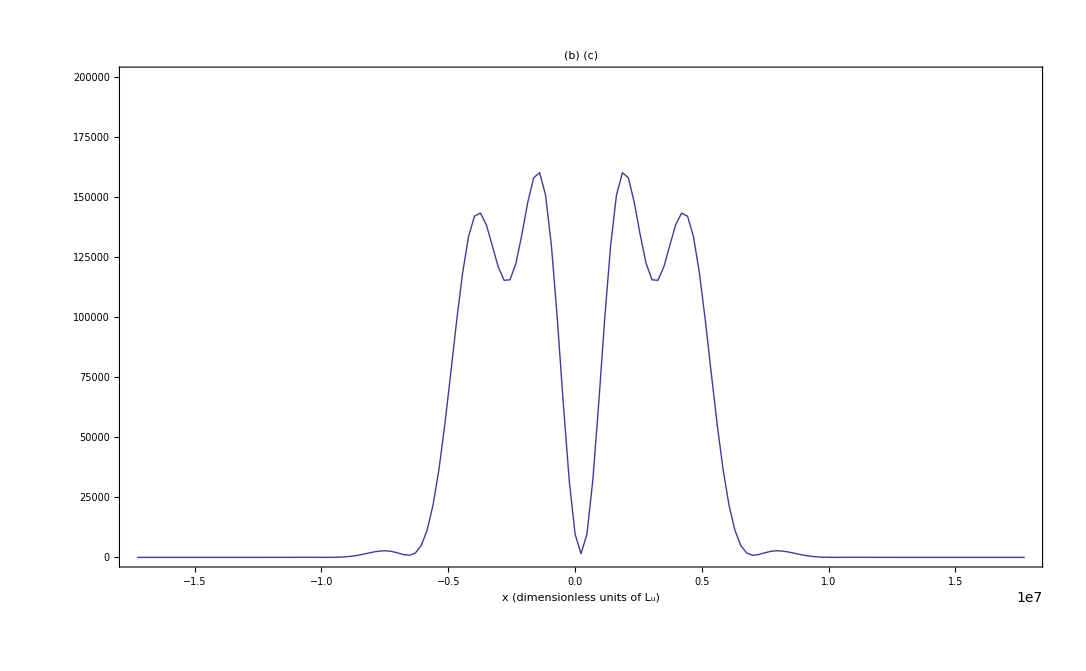

```mathematica
tofdistwithx=Table[{-edge+i*incr,tofdist[[i]]},{i,1,Length[tofdist]}];
plottofdistwithx=ListPlot[tofdistwithx,PlotJoined->True,PlotRange->{0,200000},Frame->True, Axes->False, PlotLabel->"(b) (c) ",FrameLabel->{{"",""},{"x  (dimensionless units of L_u)",""}},TextStyle-> {FontFamily-> "Bitstream Vera Sans",FontSize-> 20}]
```

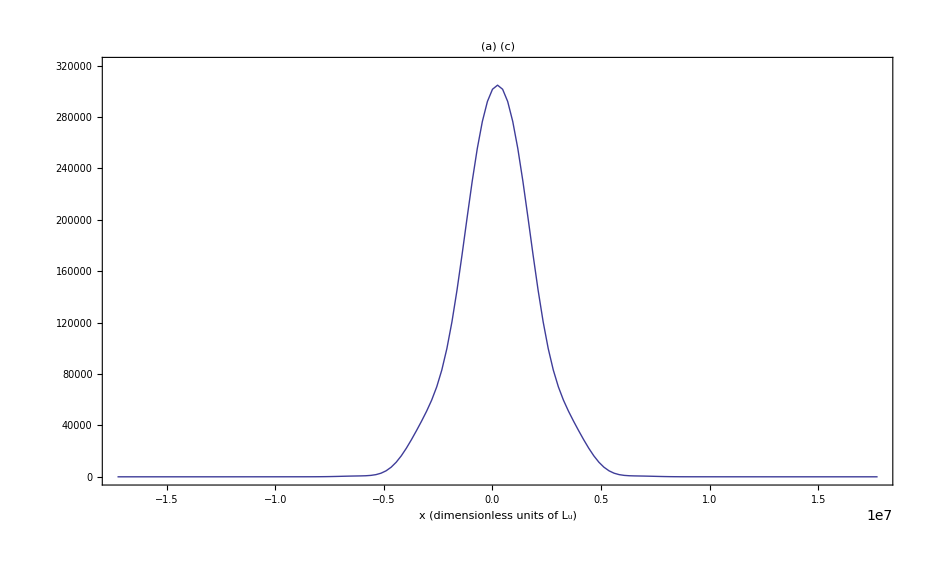

```mathematica
tofstate1tonks=Show[plottofdistwithx]
```

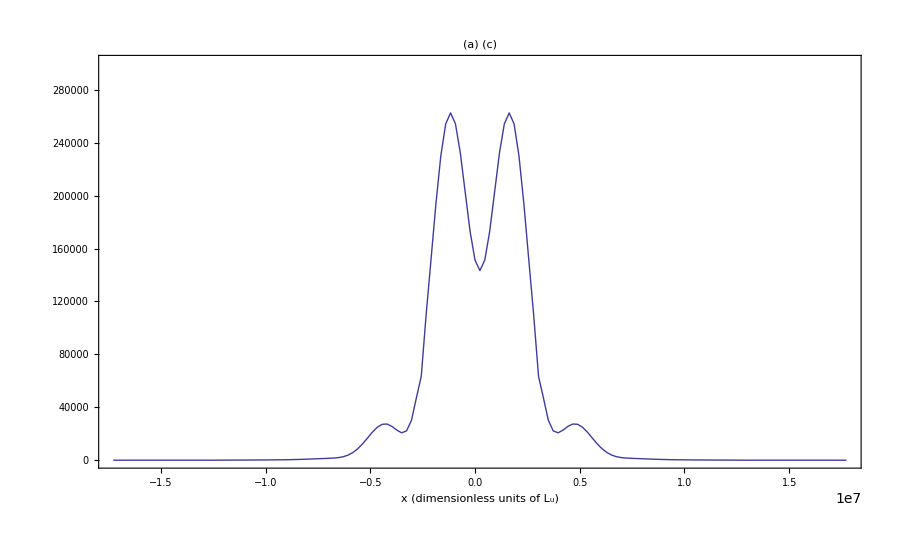

```mathematica
tofstate2tonks=Show[plottofdistwithx]
```

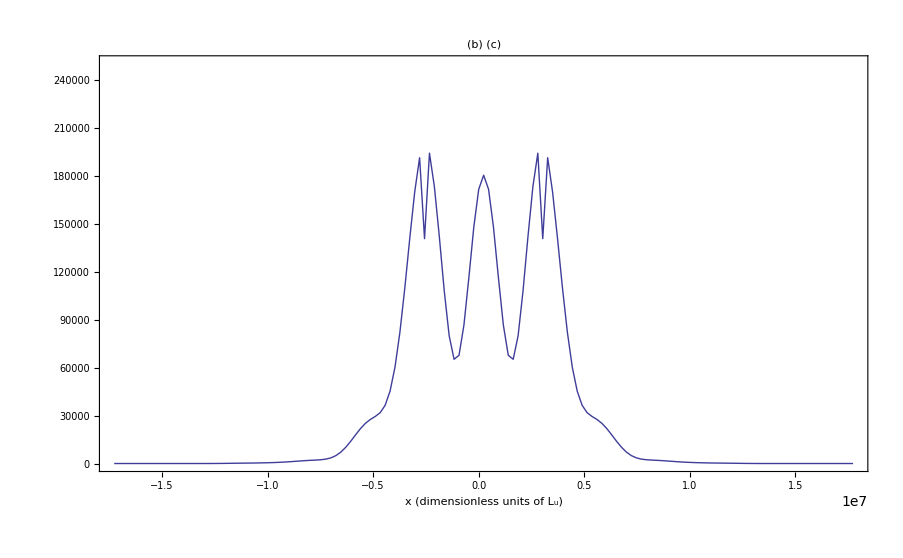

```mathematica
tofstate4tonks=Show[plottofdistwithx]
```

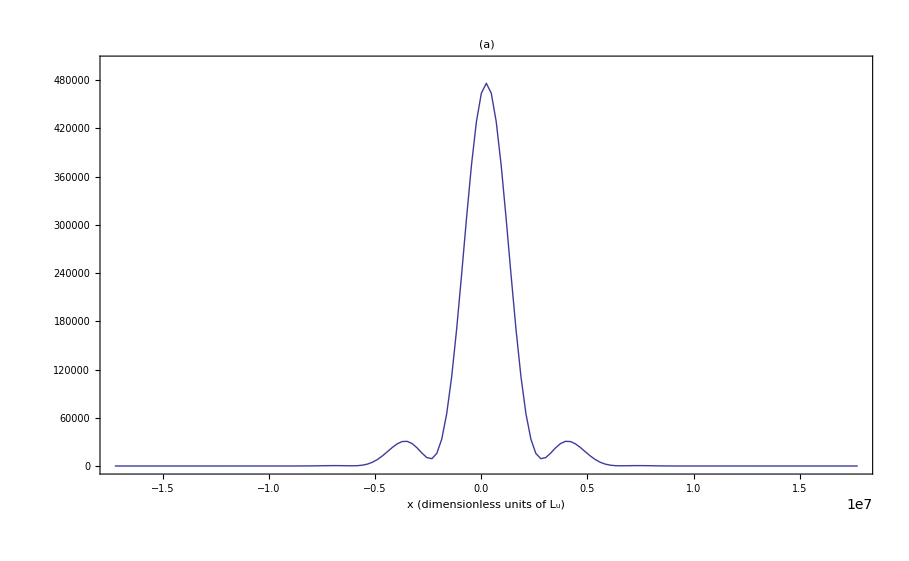

```mathematica
tofstate1=Show[plottofdistwithx]
```

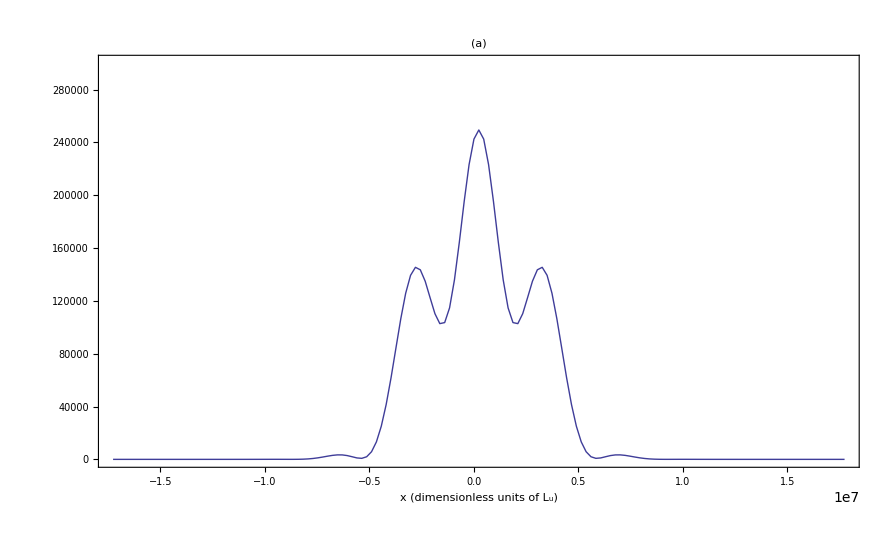

```mathematica
tofstate4=Show[plottofdistwithx]
```

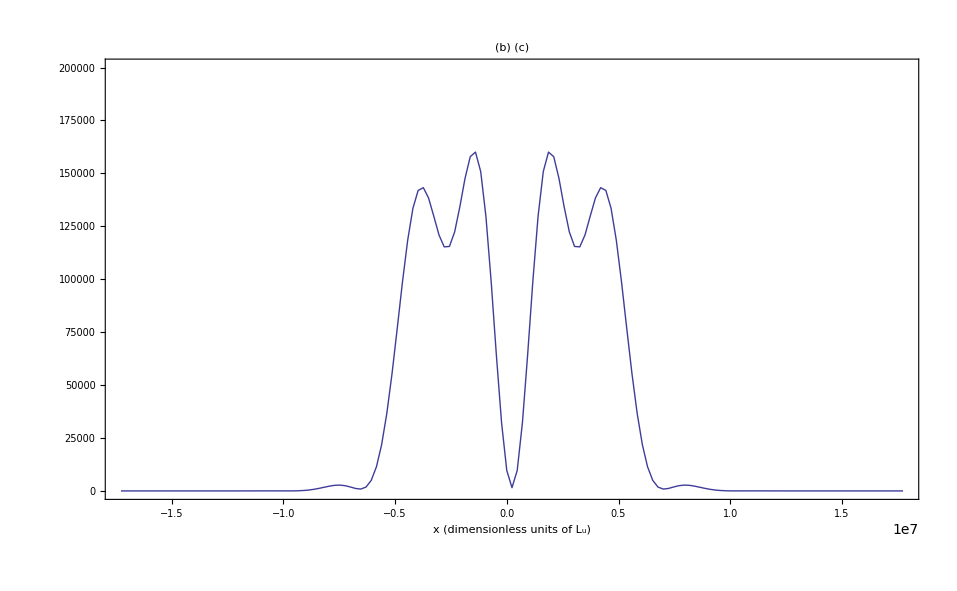

```mathematica
tofstate7=Show[plottofdistwithx]
```

0.+1.05879×10^-22 ⅈ

Integrate::idiv: Integral of Cos[3.5` u]/1.5707963267948966`  + 3.5` u does not converge on {-∞, ∞}.

∫_(-∞)^∞ Cos[3.5 u]/(π/2+3.5 u)ⅆu

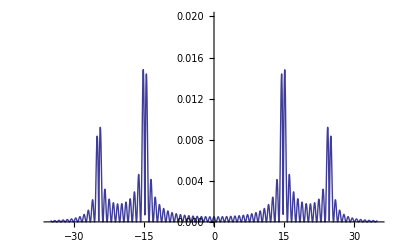

-0.746353 ⅈ ((ⅈ Cos[3.5 x])/(-π/2+3.5 x)-(ⅈ Cos[3.5 x])/(π/2+3.5 x))

```mathematica
NIntegrate[Conjugate[psiFT[253,x]]*psiFT[252,x],{x,-1,1}]
```

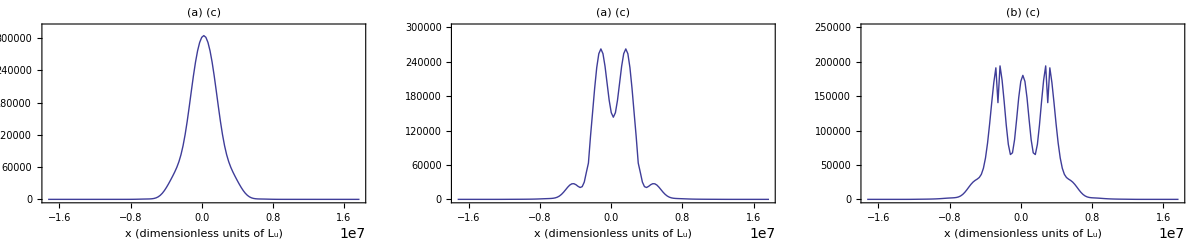

```mathematica
tofstatestonks={tofstate1tonks,tofstate2tonks,tofstate4tonks};
Show[GraphicsArray[tofstatestonks]]
```

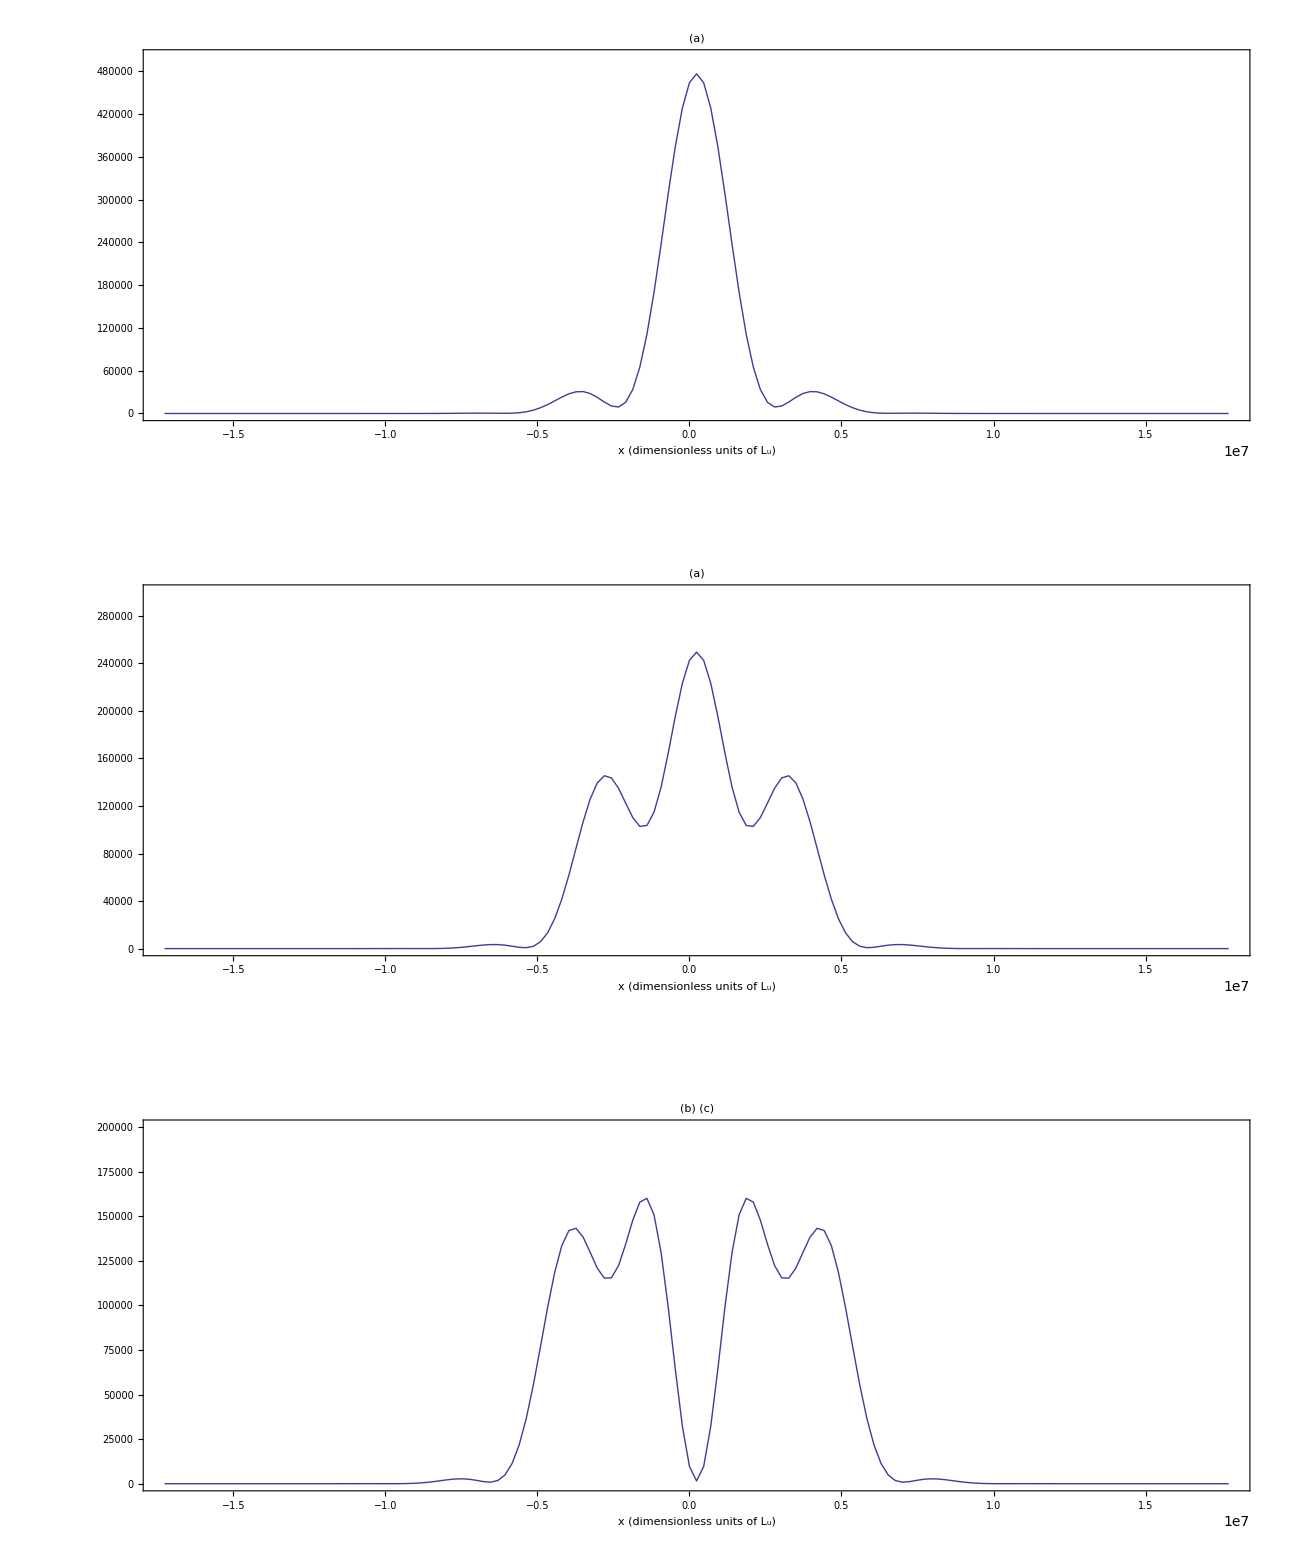

```mathematica
tofstates={{tofstate1},{tofstate4},{tofstate7}};
Show[GraphicsArray[tofstates]]
```

```mathematica
1-Graphics-
```

-Graphics-

```mathematica
NIntegrate[Abs[WavefunctionFT[u1,u2]]^2,{u1,-cutoff,cutoff},{u2,-cutoff,cutoff},AccuracyGoal->5]
```

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

0.99994

80.

```mathematica
NIntegrate[NumDenDFT[x,tau],{x,-cutoff,cutoff},AccuracyGoal->5]
```

NIntegrate::inumr: The integrand Abs[« 1 »]^2 has evaluated to non-numerical values for all sampling points in the region with boundaries {{-280.`, 280.`}}.

General::stop: Further output of NIntegrate will be suppressed during this calculation.

$Aborted